```mathematica
Length[deps3]
```

100

```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression];Length[deps3]
```

2436995

```mathematica
dops3=Map[{Chrom[#[[1]]]/24,Chrom[#[[2]]]/24, #[[1]],#[[2]],#[[3]]}&,deps3];Length[dops3]
```

2436995

```mathematica
Take[dops3,-5]
```

{{1,5,58716,395243,{3,3<->9,3<->13}},{1,1,58716,398427,{3,7<->9,5<->7}},{1,1,58716,398413,{3,7<->9,5<->9}},{1,5,58716,395251,{3,3<->6,3<->12}},{1,1,58716,398408,{3,4<->11,5<->11}}}

```mathematica
398438
```

```mathematica
VertexCount[ReadGrof[58717]]
```

14

```mathematica
thirteen=Select[dops3,1555<=#[[3]]<9151&];Length[thirteen]
```

279386

```mathematica
Max[Map[#[[2]]&,thirteen]]
```

172

```mathematica
Select[thirteen,#[[2]]==172&]
```

{{85,172,8549,57279,{3,2<->7,1<->7}},{172,172,9149,57279,{3,1<->5,1<->10}},{1,172,9150,57279,{3,1<->5,3<->5}}}

8549

9149

9150

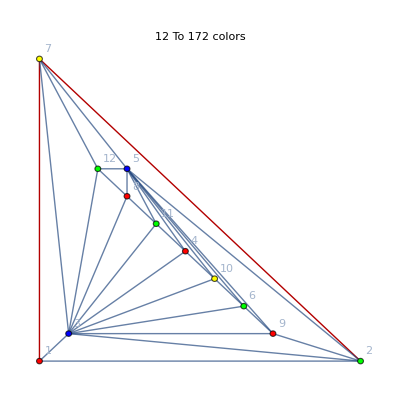
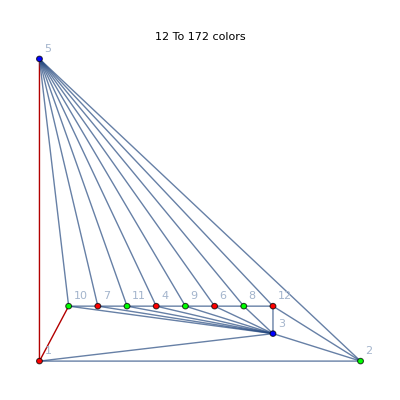
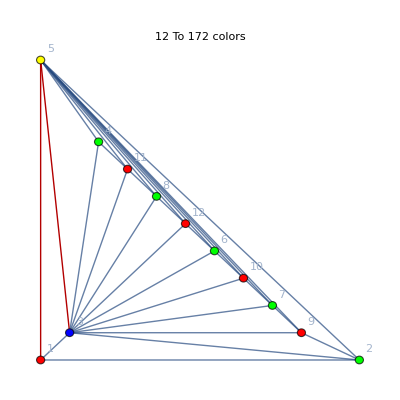

```mathematica
Map[
With[
{vars=Rest[Read[StringToStream[#[[5]]]]]},
Print[#[[3]]];PaintGraph2First[ReadGrof[#[[3]]],"x1==1&&x2==2&&x3==3",VertexLabels->"Name", 
ImageSize->400,
GraphHighlight->{vars[[1]],vars[[2]]},
PlotLabel->ToString[VertexCount[ReadGrof[#[[3]]]]]<>" To "<> ToString[#[[2]]]<>" colors "]
]&,
Select[thirteen,#[[2]]==172&]
]
```

```mathematica
fourteen=Select[dops3,9151<=#[[3]]<=58717&];Length[fourteen]
```

2113290

```mathematica
Max[Map[#[[2]]&,fourteen]]
```

341

```mathematica
Select[fourteen,#[[2]]==341&]
```

{{172,341,57279,394827,{3,2<->7,1<->7}},{341,341,58715,394827,{3,1<->5,1<->10}},{1,341,58716,394827,{3,1<->5,3<->5}}}

```mathematica
Table[IsomorphicGraphQ[ReadGrof[58716],JacobsThalGraph[k]],{k,4,15}]
```

{False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
VertexCount[JacobsThalGraph[10]]
```

14

```mathematica
IsomorphicGraphQ[ReadGrof[394827],JacobsThalGraph[10]]
```

False

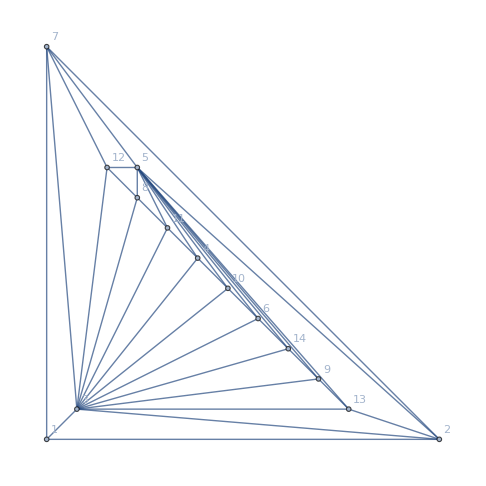

```mathematica
Graph[ReadGrof[394827],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

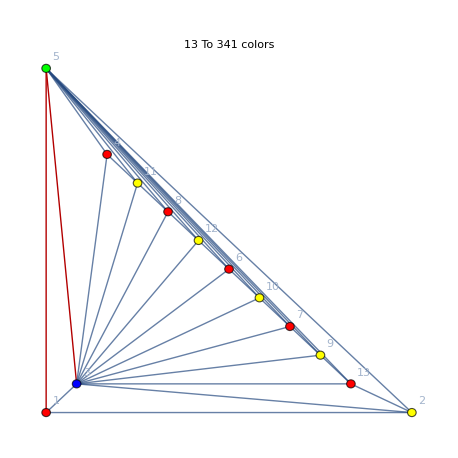

```mathematica
Map[
With[
{vars=Rest[#[[5]]]},
PaintGraph2First[ReadGrof[#[[3]]],Criterion[1<->5,3<->5],VertexLabels->"Name", 
ImageSize->400,
GraphHighlight->{1<->5,3<->5},
PlotLabel->ToString[VertexCount[ReadGrof[#[[3]]]]]<>" To "<> ToString[#[[2]]]<>" colors "]
]&,
{{1,341,58716,394827,{3,1<->5,3<->5}}}
]
```

```mathematica
Sort[EdgeList[ReadGrof[394827]]]
```

{1<->2,1<->3,1<->7,2<->3,2<->5,2<->7,2<->13,3<->4,3<->6,3<->7,3<->8,3<->9,3<->10,3<->11,3<->12,3<->13,3<->14,4<->5,4<->10,4<->11,5<->6,5<->7,5<->8,5<->9,5<->10,5<->11,5<->12,5<->13,5<->14,6<->10,6<->14,7<->12,8<->11,8<->12,9<->13,9<->14}

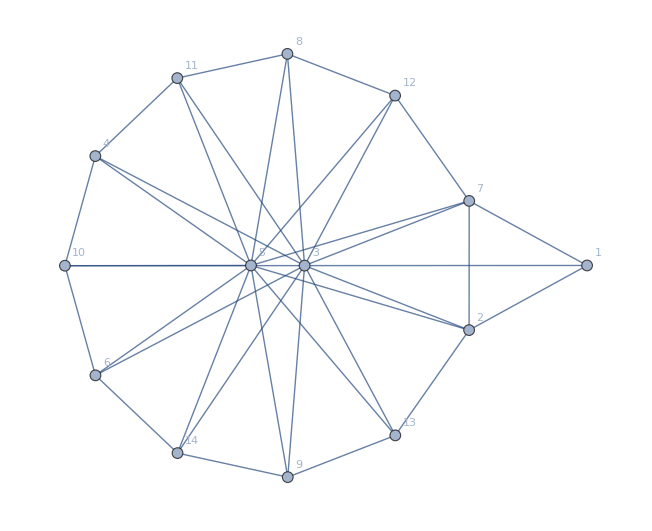

```mathematica
Graph[ReadGrof[394827],VertexLabels->"Name"]
```